## Lesson

Important date/datetime objects:

```mathematica
Now
Yesterday
Today
Tomorrow
```

Thu 29 Aug 2024 17:03:50GMT+1

Wed 28 Aug 2024

Thu 29 Aug 2024

Fri 30 Aug 2024

List dates between two dates:

```mathematica
DayRange[DateObject[{2024,8,28},"Day"],DateObject[{2024,8,30},"Day"]]
```

{Wed 28 Aug 2024,Thu 29 Aug 2024,Fri 30 Aug 2024}

Get name of the day of the week:

```mathematica
DayName[DateObject[{2024,8,30},"Day"]]
```

Friday

Moon phase on given date:

```mathematica
MoonPhase[DateObject[{2024,8,30},"Day"]]
```

0.1585

Sunrise time at location:

```mathematica
Sunrise[Here,Today]
```

Minute: Thu 29 Aug 2024 06:19GMT+1

Sunset time at location:

```mathematica
Sunset[Here,Today]
```

Minute: Thu 29 Aug 2024 20:02GMT+1

Current time at location:

```mathematica
LocalTime[Here]
```

Thu 29 Aug 2024 17:11:38GMT+1

Add dates together:

```mathematica
DatePlus[Today,-Quantity[1,"Weeks"]]
```

Thu 22 Aug 2024

Get time series of air temperatures at a location:

```mathematica
AirTemperatureData[Here,{DatePlus[Today,-Quantity[1,"Weeks"]],Now}]
```

TimeSeries[…]

Plot a time series:

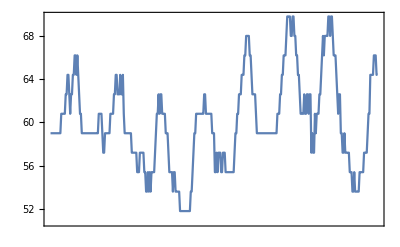

```mathematica
DateListPlot[AirTemperatureData[Here,{DatePlus[Today,-Quantity[1,"Weeks"]],Now}]]
```

Get time series for word frequency:

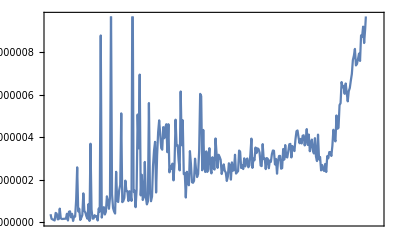

```mathematica
DateListPlot[WordFrequencyData["sauce","TimeSeries"]]
```

## Questions

Q1. Compute how many days have elapsed since January 1, 1900.

```mathematica
DateDifference[DateObject[{1900,1,1},"Day"],Today]
```

45531 days

Q2. Compute what day of the week January 1, 2000 was.

```mathematica
DayName[DateObject[{2000,1,1},"Day"]]
```

Saturday

Q3. Find the date a hundred thousand days ago.

```mathematica
DatePlus[Today,-Quantity[100000, "Days"]]
```

Sat 14 Nov 1750

Q4. Find the local time in Delhi.

```mathematica
LocalTime[Entity["City",{"Delhi","Delhi","India"}]]
```

Thu 29 Aug 2024 21:53:44GMT+5.5

Q5. Find the length of daylight today by subtracting today’s sunrise from today’s sunset.

```mathematica
Sunset[Here,Today]-Sunrise[Here,Today]
```

823 min

Q6. Generate an icon for the current phase of the moon.

```mathematica
MoonPhase["Icon"]
```

-Graphics-

Q7. Make a list of the numerical phase of the moon for each of the next 10 days.

```mathematica
MoonPhase[Today+Quantity[#,"Days"]]&/@Range[10]
```

{0.1585,0.0923,0.04329,0.01256,0.0005753,0.007175,0.03168,0.07297,0.1296,0.1998}

Q8. Generate a list of icons for the moon phases from today until 10 days from now.

```mathematica
MoonPhase[Today+Quantity[#,"Days"],"Icon"]&/@Range[0,10]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Q9. Compute the time today between sunrise in New York City and in London.

```mathematica
Sunrise[Entity["City",{"NewYork","NewYork","UnitedStates"}],Today]-Sunrise[Here,Today]
```

301 min

Q10. Find the air temperature at the Eiffel Tower at noon yesterday.

```mathematica
AirTemperatureData[Entity["Building","EiffelTower::5h9w8"],DateObject[Yesterday, TimeObject[{12, 0, 0}]]]
```

84.2 °F

Q11. Plot the temperature at the Eiffel Tower over the past week.

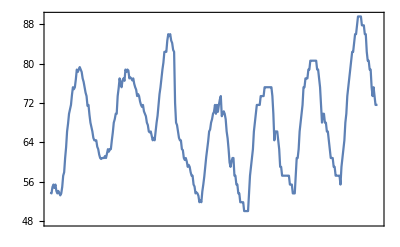

```mathematica
DateListPlot[AirTemperatureData[Entity["Building","EiffelTower::5h9w8"],{DatePlus[Today, -Quantity[1, "Weeks"]],Today}]]
```

Q12. Find the difference in air temperatures between Los Angeles and New York City now.

```mathematica
AirTemperatureData[Entity["City",{"LosAngeles","California","UnitedStates"}],Now]-AirTemperatureData[Entity["City",{"NewYork","NewYork","UnitedStates"}],Now]
```

-7. °F

Q13. Plot the historical frequency of the word “groovy”.

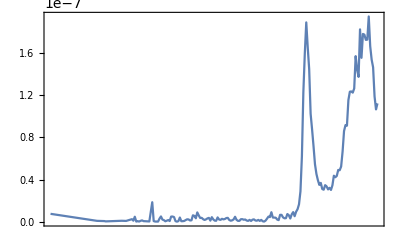

```mathematica
DateListPlot[WordFrequencyData["groovy","TimeSeries"]]
```

## Extended Questions

+Q1. Compute how many weeks have elapsed since January 1, 1900.

```mathematica
DateDifference[DateObject[{1900,1,1},"Day"],Today,"Weeks"]
```

6504.43 wk

+Q2. Compute the time between 3 pm today and sunset today.

```mathematica
Sunset[Here,Today]-DateObject[Today, TimeObject[{15}]]
```

5 h

+Q3. Generate an icon of the phase of the moon on August 29, 1959.

```mathematica
MoonPhase[DateObject[{1959,8,29},"Day"],"Icon"]
```

-Graphics-

+Q4. Make a line plot of the numerical phase of the moon for each of the next 30 days.

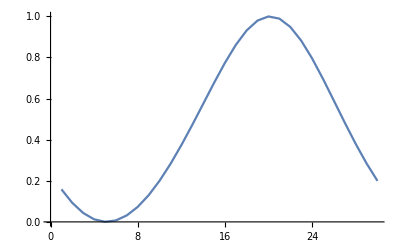

```mathematica
ListLinePlot[MoonPhase[Today+Quantity[#,"Days"]]&/@Range[30]]
```

+Q5. Make a Manipulate of the icon for the moon phase over the next 15 days.

```mathematica
Manipulate[MoonPhase[Today+Quantity[i,"Days"],"Icon"],{i,1,15,1}]
```

+Q6. Show in a column the times of sunrise for 10 days, starting today.

```mathematica
Column[Sunrise[Today+Quantity[#,"Days"]]&/@Range[0,10]]
```

Minute: Thu 29 Aug 2024 06:19GMT+1
Minute: Fri 30 Aug 2024 06:21GMT+1
Minute: Sat 31 Aug 2024 06:22GMT+1
Minute: Sun 1 Sep 2024 06:24GMT+1
Minute: Mon 2 Sep 2024 06:25GMT+1
Minute: Tue 3 Sep 2024 06:27GMT+1
Minute: Wed 4 Sep 2024 06:29GMT+1
Minute: Thu 5 Sep 2024 06:30GMT+1
Minute: Fri 6 Sep 2024 06:32GMT+1
Minute: Sat 7 Sep 2024 06:33GMT+1
Minute: Sun 8 Sep 2024 06:35GMT+1

+Q7. Plot together the historical frequencies of the words “science” and “technology”.

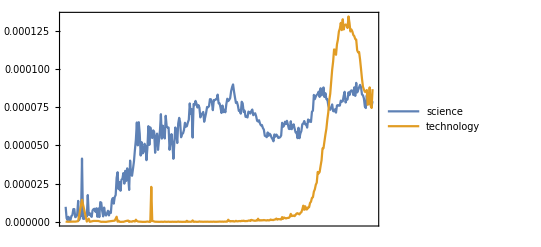

```mathematica
DateListPlot[WordFrequencyData[{"science","technology"},"TimeSeries"]]
```